## Functions

```mathematica
UncertaintyPlus[{a_,σa_},X:{_,_}...]:=Fold[{#1[[1]]+#2[[1]],√((#1[[2]])^2+(#2[[2]])^2)}&,{a,σa},{X}]
UncertaintySubtract[{a_,σa_},{b_,σb_}]:={a-b,√(σa^2+σb^2)}
UncertaintyTimes[{a_,σa_},X:{_,_}...]:=Fold[{#1[[1]] #2[[1]],Abs[#1[[1]] #2[[1]]] √(((#1[[2]])/(#1[[1]]))^2+((#2[[2]])/(#2[[1]]))^2)}&,{a,σa},{X}]
UncertaintyDivide[{a_,σa_},{b_,σb_}]:={a/b,Abs[a/b] √((σa/a)^2+(σb/b)^2)}
```

### Importing

```mathematica
BuildFilePath[root_,date_,file_]:=root<>date<>"/"<>file<>"/"<>file<>".txt"
```

```mathematica
ImportDataFile[pathToFile_]:=Module[{nans,rawData},
nans=ConstantArray["nan",4];
rawData=Import[pathToFile,"Data"];
Developer`ToPackedArray/@Round/@Rest/@Most@Split[Prepend[rawData,nans],(#2=!=nans)&]
]
```

```mathematica
ImportDataFiles[pathToFiles_]:=Join@@(ImportDataFile/@pathToFiles)
```

### Cleaning

```mathematica
CompensateDetectorLags[data_,lags_,lenStirap_]:=Module[{rules},

rules=Append[Rule@@@lags,_Integer:>0];

Function[{m},
With[{ls=m[[;;,1]]/.rules},
Transpose[{
m[[;;,1]],
Mod[m[[;;,2]]-ls,lenStirap],
m[[;;,3]]-ls,
m[[;;,4]]-UnitStep[ls-m[[;;,2]]]
}]
]
]/@data
]
```

### Filtering

```mathematica
(*Choosing to have crit@ rather than crit/@, crit must be Listable? Followup - indeed this seems to be the case, crit must be able to take a list (or is it list of lists...?)*)
FilterByCriteria[data_,columnSpec_, crit_,results_List]:=Pick[data,crit@data[[;;,;;,columnSpec]],#]&/@results
FilterByCriteria[data_,columnSpec_, crit_,result_]:=Pick[data,crit@data[[;;,;;,columnSpec]],result]

(*A slightly faster, Listable, implementation of a Between function, only valid for Integers and returns 1 for in range, 0 for below and 2 for above (Between returns True or False). *)
FastBetween[x_,{min_,max_}]:=UnitStep[x-min]+UnitStep[x-max-1]

FilterByDetector[data_,detectors_]:=FilterByCriteria[data,1,Identity,detectors]
FilterByPulseParities[data_,parities_List]:=FilterByCriteria[data,4,#,True]&/@parities
FilterByPulseParities[data_,parity_]:=FilterByCriteria[data,4,parity,True]
FilterByPulseRange[data_,{min_,max_}]:=FilterByCriteria[data,4,FastBetween[#,{min,max}]&,1]
FilterByStirapRange[data_,{min_,max_}]:=FilterByCriteria[data,2,FastBetween[#,{min,max}]&,1]
```

```mathematica
CorrelatedDetections[data_,det1_,det2_,i_Integer]:=Module[{allDetectionPairs},
First@CorrelatedDetections[data,det1,det2,{i}]
]

CorrelatedDetections[data_,det1_,det2_,idx_List]:=Module[{allDetectionPairs},
allDetectionPairs=If[det1==det2,
Flatten[Subsets[#,{2}]&/@FilterByDetector[data,det1],1],
Flatten[Outer[List,#[[1,;;]],#[[2,;;]],1]&/@Transpose[FilterByDetector[data,{det1,det2}]],2]
];

With[{detectionPulseNumberDiffs=allDetectionPairs[[;;,1,4]]-allDetectionPairs[[;;,2,4]]},
Pick[allDetectionPairs,detectionPulseNumberDiffs,#]&/@idx
]
]
```

```mathematica
(*FilterPairsByArrival[detectionPairs_,FirstOrLast_/;MemberQ[{First,Last},FirstOrLast]]:=FirstOrLast@Transpose[SortBy[#,#[[3]]&]&/@detectionPairs]*)
```

```mathematica
(*Options[FilterCorrelationPairs]={
"FirstOrLast"->(Flatten[#,1]&),
"Detector"->_,
"Parity"->(Map[True&,#]&)
};

FilterCorrelationPairs[correlationPairs_,OptionsPattern[]]:=
FilterByPulseParities[FilterByDetector[{OptionValue["FirstOrLast"][Transpose[SortBy[#,#[[3]]&]&/@correlationPairs]]},OptionValue["Detector"]],OptionValue["Parity"]]*)
```

```mathematica
Options[FilterCorrelationPairs]={
"FirstOrLast"->"Either",
"Detector"->"Either",
"Parity"->"Either"
};

FilterCorrelationPairs[correlationPairs_,OptionsPattern[]]:=Module[{correlationSingles},
correlationSingles=List@If[
OptionValue["FirstOrLast"]==="Either",
Flatten[correlationPairs,1],
OptionValue["FirstOrLast"][Transpose[SortBy[#,#[[3]]&]&/@correlationPairs]]
];

correlationSingles=If[
OptionValue["Detector"]==="Either",
correlationSingles,
FilterByDetector[correlationSingles,OptionValue["Detector"]]
];

correlationSingles=If[
OptionValue["Parity"]==="Either",
correlationSingles,
FilterByPulseParities[correlationSingles,OptionValue["Parity"]]
];

First@correlationSingles
]
```

### Statistics

```mathematica
HomCorrelations[data_,detPairs:{{_Integer,_Integer}..},func_:Subtract]:=Module[{assoc,emptyAssoc,flatRiffledData,ditheredDiffs,homBunches,groupbyInput},

flatRiffledData=Join@@Riffle[DeleteCases[data,{}],{{{-1,-1,-1,-1}}}];
ditheredDiffs=(Prepend[#,1]*Append[#,1])&@Differences[flatRiffledData[[;;,4]]];
homBunches=SplitBy[Pick[flatRiffledData,ditheredDiffs,0],Last];
groupbyInput=Transpose/@Flatten[Subsets[#,{2}]&/@homBunches,1];

assoc=GroupBy[groupbyInput,First->(#[[2]]&)];

emptyAssoc=AssociationThread[#->ConstantArray[{},Length[#]]]&@Union[detPairs,Reverse/@detPairs];
assoc=Merge[{assoc,emptyAssoc},Flatten[#,1]&];

Map[func@@#&,
If[SameQ@@#,assoc[#],Flatten[{assoc[#],Reverse/@assoc[Reverse@#]},1]]&/@detPairs,
{2}
]
]
```

```mathematica
Correlations[data_,det1_,det2_,column_]:=
If[det1==det2,
(#[[;;,2]]-#[[;;,1]])&@(Join@@(Subsets[#[[;;,column]],{2}]&/@FilterByDetector[data,det1])),
Flatten[
Outer[Plus,#[[1,;;,column]],-#[[2,;;,column]]]&/@Transpose[FilterByDetector[data,{det1,det2}]]
]
]
```

```mathematica
RealPhotonsPerThrow[data_,atomWindow_,backWindow_]:=Module[{nAtom,nBack,σAtom,σBack,scaleFactor},

nAtom=Length[Flatten[FilterByPulseRange[data,atomWindow],1]];
nBack=Length[Flatten[FilterByPulseRange[data,backWindow],1]];

scaleFactor=(Subtract@@atomWindow)/(Subtract@@backWindow);

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom}/Length[data];
{nBack,σBack}=scaleFactor{nBack,σBack}/Length[data];

N@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}}

]
```

```mathematica
NCorrelationsPerThrow[data_,detectors_List,idx_List,idxBack_List:Range[101,200]]:=Module[{correls,countsDet1,countsDet2,backCorrels},

{correls,backCorrels}=Transpose[
Table[
Total/@{#[[idx]],#[[idxBack]]}&@SparseArray[Rule@@@Tally[Select[Correlations[data,i,j,4],Positive]],{25000}],{i,detectors},{j,detectors}],
{2,3,1}
];

backCorrels=backCorrels/(Length[idxBack]/Length[idx]);

N@Transpose[{correls-backCorrels,√(correls+backCorrels)}/Length[data],{3,1,2}]
]
```

```mathematica
TotalCorrelationsPerThrow[data_,det1_,det2_]:=UncertaintyPlus@@Flatten[NCorrelationsPerThrow[data,{det1,det2},Range[100]],1]

PM1CorrelationsPerThrow[data_,det1_,det2_]:=UncertaintyPlus@@Flatten[NCorrelationsPerThrow[data,{det1,det2},{1}],1]
```

### Plotting

```mathematica
LabelledMOTHistogram[data_,atomLims_,notAtomLims_]:=Module[{binWidth,nNotAtoms,backLevel,nBins=50},

nNotAtoms=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,notAtomLims]];
backLevel= nNotAtoms/(nBins((#[[2]]-#[[1]]&)@notAtomLims)/motPlotMax);
backLevel=backLevel/(Length[data](motPlotMax photonLength 10^-12/10^-3)/nBins);

Histogram[Flatten[data[[;;,;;,4]]],{0,motPlotMax,motPlotMax/nBins},Function[{bins,counts},counts/(Length[data](motPlotMax photonLength 10^-12/10^-3)/nBins)],
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^9}]&@Range[0,motPlotMax,motPlotMax/5]}},
Epilog->{
Dashed,Line[{{0,backLevel},{motPlotMax,backLevel}}],Opacity[0.2],
Green,Rectangle[Scaled[{atomLims[[1]]/motPlotMax,0}],Scaled[{atomLims[[2]]/25*^3,1}]],Red,Rectangle[Scaled[{notAtomLims[[1]]/motPlotMax,0}],Scaled[{notAtomLims[[2]]/motPlotMax,1}]]
},
FrameLabel->{{"Counts per Throw per ms",None},{"Pulse Number","MOT time / ms"}},
AspectRatio->1/2,
genOpts
]
]
```

```mathematica
LabelledG2Histogram[data_,det1_,det2_]:=Module[{correls11,correls12,correls22,bc11,bc12,bc22,lspData11,lspData12,lspData22,EpiLabelF},

correls11=Developer`ToPackedArray@Correlations[data,det1,det1,4];
correls12=Developer`ToPackedArray@Correlations[data,det1,det2,4];
correls22=Developer`ToPackedArray@Correlations[data,det2,det2,4];

bc11=BinCounts[-correls11,{-binLimit,1}];
bc12=BinCounts[correls12,{-binLimit,binLimit+1}];
bc22=BinCounts[correls22,{0,binLimit+1}];
{bc11,bc12,bc22}/=Length[data];

{lspData11,lspData12,lspData22}=
{
Riffle[#[[1;;;;2]],0],
Riffle[#[[2;;;;2]],0,{1,-1,2}]
}&/@{bc11,bc12,bc22};

EpiLabelF[{d1_,d2_},{x_,y_}]:=Text[StringForm["Det `1` - Det `2`",d1, d2],Scaled[{x,y}],Scaled[Round[{x,y},0.05]],Background->Directive[Opacity[0.8],White]];

With[{opts=Sequence[
PlotRange->{All,{0,5Ceiling[Max[{bc11,bc12,bc22}]/5.,0.001]}},
PlotStyle->None,
Filling->{1->{Axis,Directive[Opacity[0.7],ColorData[97][4]]},2->{Axis,Directive[Opacity[0.7],ColorData[97][1]]}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
genOpts
]},
Row@{
ListStepPlot[lspData11,"Center",DataRange->{-binLimit,0},AspectRatio->1,Epilog->{EpiLabelF[{det1,det1},{0.02,0.98}]},
FrameLabel->{{"Correlatoins per MOT throw",None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts],
ListStepPlot[lspData12,"Center",DataRange->{-binLimit,binLimit},AspectRatio->1/2,Epilog->{EpiLabelF[{det1,det2},{0.02,0.98}]},
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts],
ListStepPlot[lspData22,"Center",DataRange->{0,binLimit},AspectRatio->1,Epilog->{EpiLabelF[{det2,det2},{0.98,0.98}]},
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts]
}
]
]
```

```mathematica
LabelledG2HistogramTriangle[data_,detectors_]:=Module[{IdxT,correls,bc,lsp,EpiLabelF},

IdxT[{i_,j_}]:={i,i+j-1};

correls=Table[Developer`ToPackedArray@Correlations[data,detectors[[i]],detectors[[j]],4],{i,1,Length[detectors]},{j,i,Length[detectors]}];

bc=MapIndexed[
If[Equal@@IdxT[#2],
BinCounts[-#1,{-binLimit,1}],
BinCounts[#1,{-binLimit,binLimit+1}]
]/Length[data]&,correls,{2}];

lsp=Map[{Riffle[#[[1;;;;2]],0],Riffle[#[[2;;;;2]],0,{1,-1,2}]}&,bc,{2}];

EpiLabelF[{d1_,d2_},{x_,y_}]:=Text[StringForm["Det `1` - Det `2`",d1, d2],Scaled[{x,y}],Scaled[Round[{x,y},0.05]],Background->Directive[Opacity[0.8],White]];

With[{opts=Sequence[
PlotRange->{All,{0,5Ceiling[Max[bc]/5.,0.001]}},
PlotStyle->None,
Filling->{1->{Axis,Directive[Opacity[0.7],ColorData[97][4]]},2->{Axis,Directive[Opacity[0.7],ColorData[97][1]]}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
genOpts
]},
Grid[PadLeft[#,Length[detectors],Null]&/@MapIndexed[
ListStepPlot[#1,"Center",DataRange->If[Equal@@IdxT[#2],{-binLimit,0},{-binLimit,binLimit}],AspectRatio->1,Epilog->{EpiLabelF[{detectors[[IdxT[#2][[1]]]],detectors[[IdxT[#2][[2]]]]},{0.02,0.98}]},
FrameLabel->{{"Correlatoins per MOT throw",None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts]&,
lsp,
{2}
]
]
]
]
```

```mathematica
StirapSubHistogram[data_,atomWindow_,backWindow_,nbins_,col_,opts:OptionsPattern[]]:=Module[{dataAtom,dataBack,nAtom,nBack,σAtom,σBack,N1,N2,bc,backLvl,amp,limitedPhotonLength},

limitedPhotonLength=-Subtract@@stirapLimits;

dataAtom=Flatten[FilterByPulseRange[data,atomWindow][[;;,;;,2]]];
dataBack=Flatten[FilterByPulseRange[data,backWindow][[;;,;;,2]]];

nAtom=Length[dataAtom];
nBack=Length[dataBack];

σAtom=√nAtom;
σBack=√nBack;

N1=N@Length[data];
N2=limitedPhotonLength/nbins 10^-6;

{nAtom,σAtom}={nAtom,σAtom}/N1;
{nBack,σBack}=(Subtract@@atomWindow)/(Subtract@@backWindow){nBack,σBack}/N1;

bc=BinCounts[dataAtom,{0.,limitedPhotonLength,limitedPhotonLength/nbins}]/(N1 N2);

backLvl=(nBack/nbins)/N2;
amp=(Max[bc]-backLvl);

ListStepPlot[bc,"Center",DataRange->{0.,limitedPhotonLength/1000.},
PlotStyle->Directive[AbsoluteThickness[0.8],Black],
Filling->{1->{Axis,col}},
Epilog->{
{Opacity[0.5],Black,Rectangle[{0,0},{limitedPhotonLength/1000,backLvl}]},
{First@Plot[{
backLvl+amp Sin[π x/(photonLength/1000)]^2,
backLvl+amp Sin[π x/(photonLength/1000)]^4
},{x,0,photonLength/1000},PlotStyle->{Directive[Black,Opacity[0.5],Dotted],Directive[Black,Opacity[0.5],Dashed]}]},
{Text[StringRiffle[UncertaintyForm[#,1]&/@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}},"\n"],Scaled[{0.98,0.98}],Scaled[{1,1}],Background->Directive[Opacity[1],White]]}
},
opts
]
]
```

```mathematica
TotalGrid[g_,f_:Total]:=ArrayFlatten[{{g,{Map[f,g]}ᵀ},{{Map[f,gᵀ]},{{f@Flatten[g,1]}}}},2]
```

```mathematica
DetectionGrid[data_,detectors_]:=Module[{subdividedData,subdividedDataGrid,nbins,max,hopts,cols,frameLabels},

subdividedData=FilterByDetector[#,detectors]&/@FilterByPulseParities[data,{EvenQ,OddQ}];
subdividedDataGrid=TotalGrid[subdividedData,Map[Join@@#&,Transpose@#]&];

nbins=20;
max=Max[HistogramList[Flatten[#[[;;,;;,2]]],{0,photonLength,photonLength/20}][[2]]&/@Join[subdividedDataGrid[[;;2,3]],subdividedDataGrid[[3,;;2]]]];
hopts=Sequence[Frame->True,GridLines->Automatic,PlotRangePadding->None,PlotRange->{{0,photonLength/1000.},{0,5Ceiling[max/5.]/($NTHROWS photonLength/nbins 10^-6)}},ImageSize->200,AspectRatio->0.8];

cols=Map[ColorData[97],{{4,Sequence@@ConstantArray[1,Length[detectors]-1],3},{4,Sequence@@ConstantArray[1,Length[detectors]-1],3},{2,Sequence@@ConstantArray[2,Length[detectors]-1],5}},{2}];

frameLabels={{
{{"Evens",None},{None,"Detector "<>ToString[detectors[[1]]]}},
Sequence@@({{"",None},{None,"Detector "<>ToString[#]}}&/@detectors[[2;;]]),
{{"",None},{None,"All Detectors"}}
},{
{{"Odds",None},{None,""}},
Sequence@@ConstantArray[{{"",None},{None,""}},{6}]
},{
{{"Both Parities",None},{None,""}},
Sequence@@ConstantArray[{{"",None},{None,""}},{6}]
}};

Grid@MapIndexed[
StirapSubHistogram[#1,atomWindow,backWindow,nbins,cols[[Sequence@@#2]],FrameLabel->frameLabels[[Sequence@@#2]],hopts]&,
subdividedDataGrid,
{2}
]
]
```

### Formatting

```mathematica
UncertaintyForm[{a_,b_},p_:2]:=NumberForm[
SetAccuracy[a±b,Accuracy@SetPrecision[b,p]],
NumberFormat->(If[#3=!="",StringJoin[{#1,Table["0",Abs@ToExpression@#3-1]}],#1]&),
ExponentFunction->(Null&)
]//ToString//Quiet
```

```mathematica
PadDecimalStrings[string_,{l1_,lt_}]:=StringRiffle[
StringPadRight[StringRepeat[" ",l1-With[{sp=StringPosition["0","."]},If[sp==={},StringLength["0"],sp[[1,1]]]]]<>#,lt]&/@StringSplit[string][[{1,-1}]],
"±"]
```

### Derived Statistics

```mathematica
AtomsPerThrowPM1[Np_,Nc1_,T_]:=(Np^2(T-1))/(Nc1 T^2)
PhotonEfficiencyPM1[Np_,Nc1_,T_]:=(Nc1 T)/(Np (T-1))
```

```mathematica
AtomsPerThrowPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Np^2(T-1))/(Nc1 T^2),(T-1)/T^2 Np^2/Nc1 √(((2Np σNp)/Np^2)^2+(σNc1/Nc1)^2)}
PhotonEfficiencyPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Nc1 T)/(Np (T-1)),T/(T-1)Nc1/Np √((σNc1/Nc1)^2+(σNp/Np)^2)}
```

```mathematica
AtomsPerThrow[Np_,NcAll_,T_]:=(Np^2(T-1))/(2 NcAll T)
PhotonEfficiency[Np_,NcAll_,T_]:=(2 NcAll)/(Np (T-1))
```

```mathematica
AtomsPerThrow[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(Np^2(T-1))/(2 NcAll T),(T-1)/(2 T)Np^2/NcAll √(((2Np σNp)/Np^2)^2+(σNcAll/NcAll)^2)}
PhotonEfficiency[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(2 NcAll)/(Np (T-1)),2/(T-1)NcAll/Np √((σNcAll/NcAll)^2+(σNp/Np)^2)}
```

## Usage New

ToDo:
	Handle when attempting to import files which aren’t there or have no data
	Make it so that the only files listed as available to import are folder with actual data txt files in (as the folder grets created at the start of a run and the txt file at the end. (or not, Tom lines them up early)
	Including when also selsected empty folders...

### Import New

```mathematica
folderForm=__~~"-"~~__~~"-"~~__;
```

```mathematica
root="/Volumes/ALDAQ/KuhnGroup/Results017_New/data/";
```

```mathematica
root="Z:\\Results017_New\\data\\";
```

```mathematica
Panel[
Column[{
Labeled[
InputField[Dynamic[root],String],
"Root",Top],
Labeled[
PopupMenu[Dynamic[date],Reverse@(FileNameTake/@FileNames[folderForm,root])],
"Date",Left],
Labeled[Row[{
Dynamic@ListPicker[Dynamic[files],Reverse@(FileNameTake/@FileNames[folderForm,root<>date])],
Column[{
Button["Update",odate=date;date="00-00-00";date=odate;,ImageSize->{80,80}],
Button["Copy File Names",CopyToClipboard[StringRiffle[files,", "]]]
}]
}],
"Files",Left],
Button["Import",
data1Raw=ImportDataFiles[BuildFilePath[root,date,#]&/@files];,
Method->"Queued"
],

Dynamic["Length data = "<>ToString[Length[data1Raw]]]
}]
]
```

Root
Date
Update
Copy File NamesFiles
Import

### Display

#### Analysis definition

```mathematica
genOpts=Sequence[PlotRange->All,Frame->True,GridLines->Automatic,PlotRangePadding->None,ImageSize->{Automatic,320}];
```

```mathematica
ANALYSIS[data1Raw_]:=Module[{},
data2Limited=Select[data1Raw,Between[Length[#],countCutOffs]&];
data2Limited=CompensateDetectorLags[data2Limited,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];
data2Limited=FilterByStirapRange[data2Limited,stirapLimits];

$NTHROWS=Length[data2Limited];

p1=LabelledMOTHistogram[data2Limited,atomWindow,backWindow];

{Np,σNp}=RealPhotonsPerThrow[data2Limited,atomWindow,backWindow][[1]];

data3Windowed=FilterByPulseRange[data2Limited,atomWindow];

p2=ListLinePlot[Length/@data3Windowed,FrameLabel->{{"Counts",None},{"Throw Number",""}},PlotRange->{0,All},FrameTicks->{Automatic,{Automatic,All}},AspectRatio->1/2,genOpts];

g3=DetectionGrid[data2Limited,detectors];

p6=If[Length[detectors]==2,
LabelledG2Histogram[data3Windowed,detectors[[1]],detectors[[2]]],
LabelledG2HistogramTriangle[data3Windowed,detectors]
];

{NcAll,σNcAll}=TotalCorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];
{Nc1,σNc1}=PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];

pads={5,12};

infoTable=TableForm[{
{"Interaction Time:", ToString[tInter]<>"  ⟺  "<>ToString[tInter photonLength/10.^6]<>" μs"},
{"",""},
{"Number MOT Throws:", Length[data2Limited]},
{"",""},
{"Real photons per throw:", PadDecimalStrings[UncertaintyForm[{Np,σNp}],pads]},
{"All Correlations per throw:",  PadDecimalStrings[UncertaintyForm[{NcAll,σNcAll}],pads]},
{"±1 Correlations per throw:", PadDecimalStrings[UncertaintyForm[{Nc1,σNc1}],pads]},
{"",""},
{"Atoms per throw:",PadDecimalStrings[UncertaintyForm@AtomsPerThrow[{Np,σNp},{NcAll,σNcAll},tInter],pads]},
{"Photon efficiency:",PadDecimalStrings[UncertaintyForm@PhotonEfficiency[{Np,σNp},{NcAll,σNcAll},tInter],pads]}
{"",""}
(*{"Atoms per throw (±1):",PadDecimalStrings[UncertaintyForm@AtomsPerThrowPM1[{Np,σNp},{Nc1,σNc1},tInter],pads]},
{"Photon efficiency (±1):",PadDecimalStrings[UncertaintyForm@PhotonEfficiencyPM1[{Np,σNp},{Nc1,σNc1},tInter],pads]}*)
}];

Grid[{
{p1,p2,If[Length[detectors]>2,infoTable,SpanFromLeft]},
{p6,SpanFromLeft},
{g3,If[Length[detectors]==2,infoTable,SpanFromLeft],SpanFromLeft}
}]
]
```

#### Run

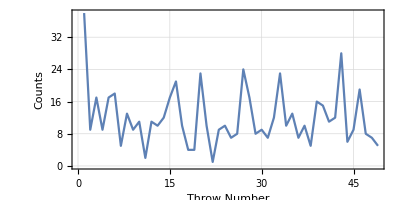
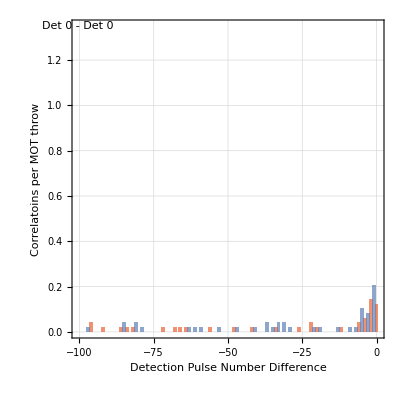
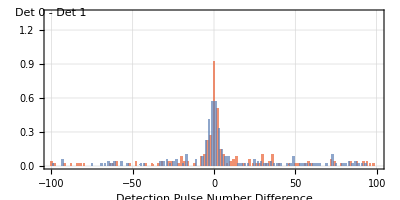
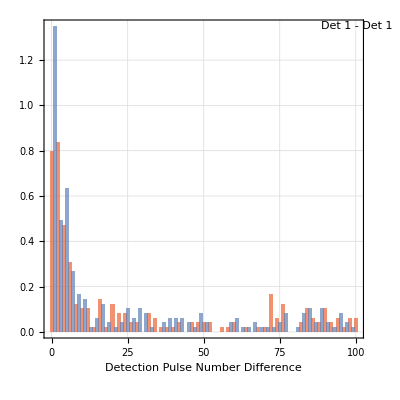
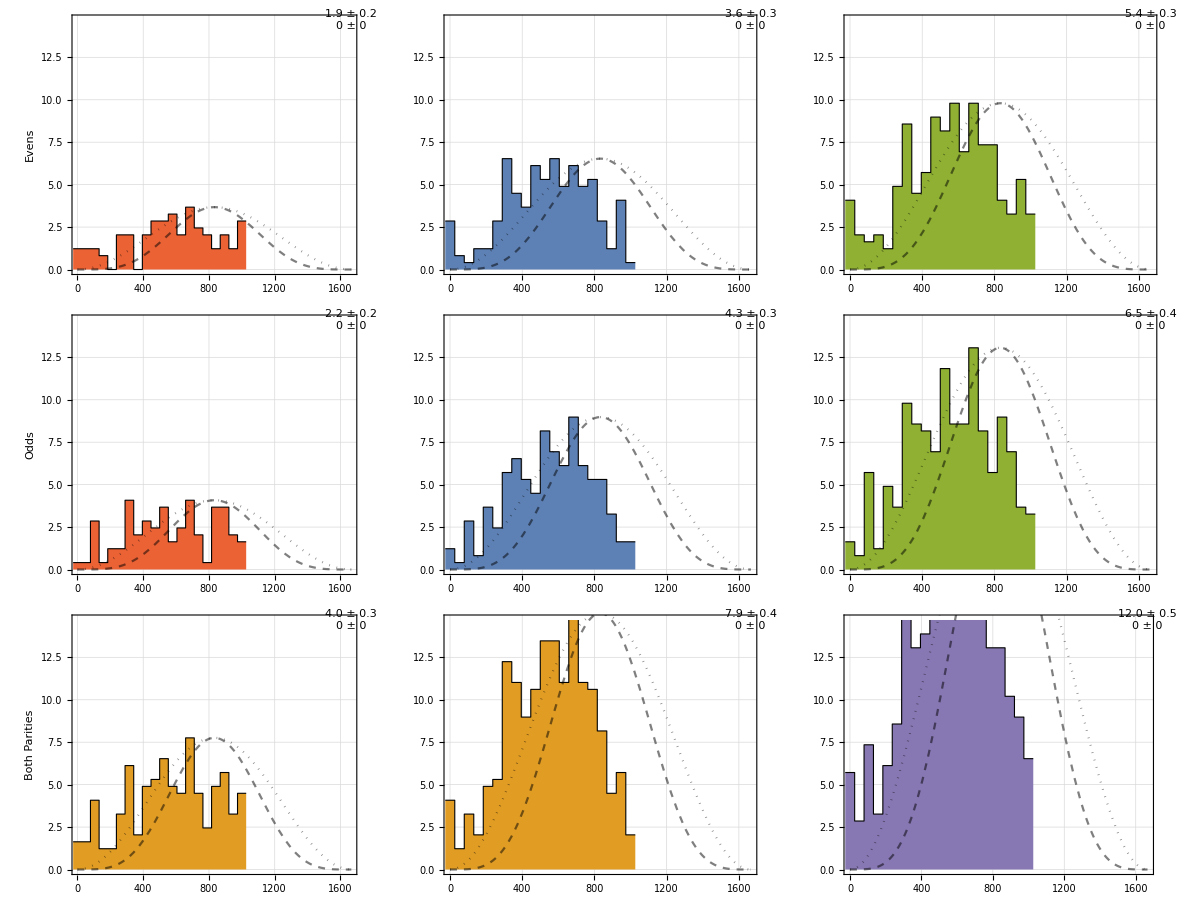
-Graphics- | -Graphics- | 
-Graphics--Graphics--Graphics- |  | 
-Graphics- | Interaction Time: | 30  ⟺  49.98 μs
 | 
Number MOT Throws: | 49
 | 
Real photons per throw: |     11.96   ±    0.49    
All Correlations per throw: |     9.57    ±    0.74    
±1 Correlations per throw: |     2.61    ±    0.24    
 | 
Atoms per throw: |     7.22    ±    0.81    
 Photon efficiency: |      0.0552  ±    0.0048   |

```mathematica
countCutOffs={1,200};

atomWindow=Round[{0.6,8}10^3];
backWindow=Round[{7,12}10^3];
motPlotMax=5000;

detectors={0,1};

lag[0]=lag[1]=lag[2]=lag[3]=lag[4]=lag[5]=lag[6]=lag[7]=lag[8]=photonLength-400*^3;

photonLength=1666*^3;
stirapLimits={0,photonLength};
stirapLimits={0,1000}*10^3;

tInter=30;

binLimit=100;(*Chose an even number*)

ANALYSIS[data1Raw]
```

### Additional Analyses

#### Conditional Efficiencies

```mathematica
nNum=(Length/@Flatten[FilterByPulseParities[{CorrelatedDetections[data3Windowed,#[[1]],#[[2]],1][[;;,1]]},{EvenQ,OddQ}],1])&/@Transpose[{detectors,Reverse[detectors]}];
nDenom=Map[Length@Flatten[#,1]&,(FilterByDetector[#,Reverse@detectors]&/@FilterByPulseParities[data2Limited,{OddQ,EvenQ}]),{2}];

tabOpts=Sequence[TableHeadings->{{"Even","Odd"},("Det "<>ToString[#])&/@detectors}];

Grid[{{
"Number of detections following a detection on the opposite detector in the previous interval",
TableForm[nNum,tabOpts]
},
{
"Number of detections on the given detector",
TableForm[nDenom,tabOpts]
},
{
"Conditional Probabilities",
TableForm[Map[UncertaintyForm[UncertaintyDivide@@#]&,Transpose[{Transpose[{nNum,√nNum},{3,1,2}],Transpose[{nDenom,√nDenom},{3,1,2}]},{3,1,2}],{2}],tabOpts]
}},
ItemSize->25,
Spacings->{0,2},
Alignment->Top
]
```

Number of detections following a detection on the opposite detector in the previous interval |  | Det 0 | Det 1
Even | 10 | 2
Odd | 5 | 8
Number of detections on the given detector |  | Det 0 | Det 1
Even | 2322 | 2082
Odd | 663 | 728
Conditional Probabilities |  | Det 0 | Det 1
Even | 0.0043 ± 0.0014 | 0.001 ± 0.00068
Odd | 0.0075 ± 0.0034 | 0.0110 ± 0.0039

#### n̄ and HOM

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,1}}][[1]];
{correlsHom00, correlsHom11}=HomCorrelations[data3Windowed,{{0,0},{1,1}}];
{nii,nij,njj}=Length/@{correlsHom00,correlsHom,correlsHom11};

N[nij/(nii+njj+nij)]
{nij,nii+njj+nij}
```

0.407407

{11,27}

{-181016,211455}

42.9677

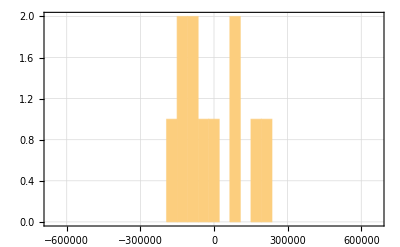

```mathematica
nbins=31;
MinMax@correlsHom
N@2photonLength*10^-3/nbins
homHist = Histogram[correlsHom,{-photonLength,photonLength,2photonLength/nbins},genOpts]
```

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,1}}][[1]];
Length@correlsHom
N@Length[correlsHom]/Length[data3Windowed]
MinMax@correlsHom
```

48

0.0963855

{-321373,420949}

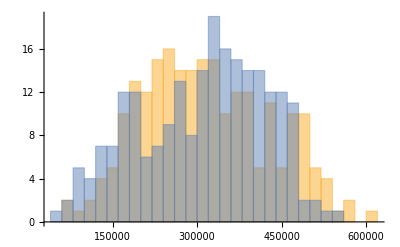

```mathematica
Histogram[Transpose@Flatten[HomCorrelations[data3Windowed,{{0,1}},List],1],21]
```

### Detection Patterns

```mathematica
keys={{0},{1},{2},{0,0},{0,2},{2,0},{1,1},{2,2},{0,2,0},{2,0,2},{0,0,0}};
m=Max[keys]+1;
lens=Union[Length/@keys];


diffs=Developer`ToPackedArray/@(Differences/@data3Windowed[[;;,;;,4]]);
as=Join@@ParallelTable[
Counts[Pick[#,UnitStep[(Max/@#)-m],0]&@(Join@@(Partition[#,l,1]&/@diffs))],
{l,lens}
];

TableForm[{keys,as/@keys},TableDepth->2,TableAlignments->Center]
```

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,0},{0,2},{2,2}}];
Length[Flatten[correlsHom]]
```

311

### G2 Table 16

```mathematica
N[Length[HomCorrelations[data3Windowed,{{0,1}}][[1]]]/Length[data3Windowed]]
UncertaintyPlus[#[[1,2]],#[[2,1]]]&@NCorrelationsPerThrow[data3Windowed,{0,1},{2}]
```

0.0758135

{0.294176,0.0109888}

```mathematica
Clear[Data16]
Data16[data_,det1_,det2_,hideIdx_List,constrainRange_:{0,50}]:=Module[{dataDet1,dataDet2,idx0,correls,key,fEven,fOdd,fBoth,fEmpties,g2DataEvenOddBothEmpty,dataEvenOddBothEmpty},

(*Remove MOT throws where no detections on a detector*)
{dataDet1,dataDet2}=FilterByDetector[data,{det1,det2}];
idx0=Union[Flatten[Position[Length/@#,0]&/@{dataDet1,dataDet2},1]];
{dataDet1,dataDet2}=Delete[#,idx0]&/@{dataDet1,dataDet2};

(*Generate key based on correlations - expand*)
correls=Outer[Plus,#[[1,;;,4]],-#[[2,;;,4]]]&/@Transpose[{dataDet1,dataDet2}];
key=Clip[Abs[correls],constrainRange,{-1,-1}];
key=Abs[correls]/.x_:>-1/;Or[MemberQ[hideIdx,x],x>constrainRange[[2]]];

fEven=Function[{list},With[{plist=Select[list,NonNegative]},If[plist==={},False,And@@(EvenQ/@plist)]]];
fOdd=Function[{list},With[{plist=Select[list,NonNegative]},If[plist==={},False,And@@(OddQ/@plist)]]];
fBoth=Function[{list},With[{plist=Select[list,NonNegative]},If[plist==={},False,ContainsAll[(EvenQ/@plist),{True,False}]]]];
fEmpties=Function[{list},And@@(Negative/@list)];

g2DataEvenOddBothEmpty=
Map[Function[{f},Join@@@Transpose[{Pick[dataDet1,(f/@#)&/@key,True],Pick[dataDet2,(f/@Transpose[#])&/@key,True]}]],{fEven,fOdd,fBoth,fEmpties}];

dataEvenOddBothEmpty=Map[FilterByDetector[#,{det1,det2}]&,g2DataEvenOddBothEmpty];

(*4x4 array of standard data objects, filtered by Even Odd Both Empty*)
Outer[
(SortBy[#,#[[3]]&]&/@(Join@@@Transpose[{#1,#2}]))&,
dataEvenOddBothEmpty[[;;,1]],
dataEvenOddBothEmpty[[;;,2]],
1
]
]
```

```mathematica
data16=Data16[data3Windowed,0,1,{0},{0,10}];
```

```mathematica
g16=ParallelMap[LabelledG2Histogram[#,det1,det2][[1,2]]&,data16,{2}];
```

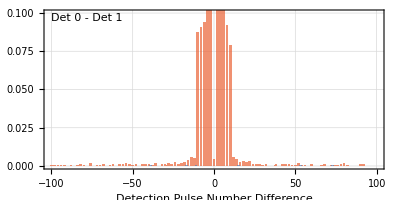
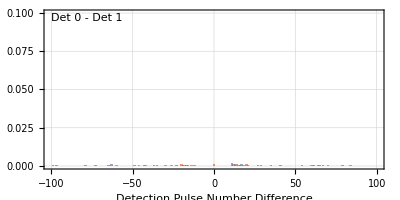
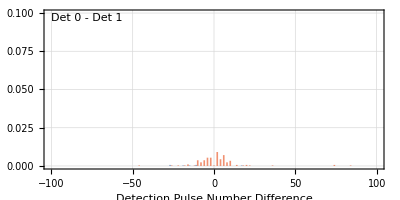
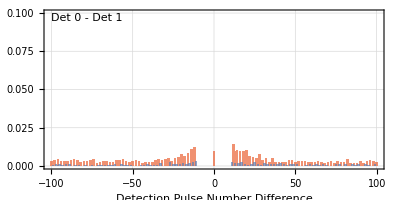
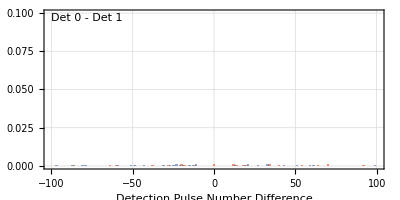
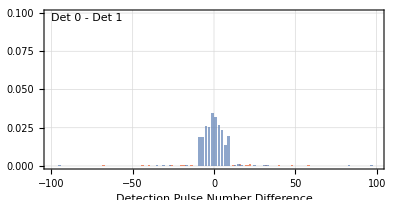
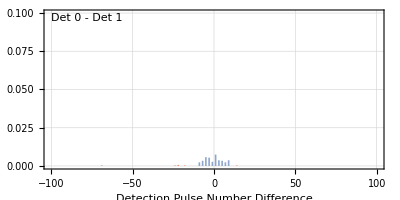
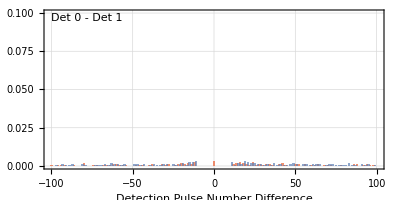
| Even | Odd | Both | Empty
Even | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Odd | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Both | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Empty | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[g16/.{Rule[ImageSize,_]:>Rule[ImageSize,400],Rule[PlotRange,{xr_,yr_}]:>Rule[PlotRange,{xr,{0,0.1}}]},TableHeadings->{{"Even","Odd","Both","Empty"},{"Even","Odd","Both","Empty"}},TableAlignments->Center]
```

### Other / Additional

```mathematica
NCorrelationsPerThrow[data3Windowed,{0,2},{1}]
```

{{{0.0146392,0.0021952},{0.0177882,0.00239569}},{{0.0184549,0.00241646},{0.0104176,0.0021557}}}

```mathematica
TableForm[
NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,1]]
]
TableForm[
NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,2]]
]
TableForm[
(#/Total[#,2])&@NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,1]]
]
```

0.0146392 | 0.0177882
0.0184549 | 0.0104176

0.0021952 | 0.00239569
0.00241646 | 0.0021557

0.238813 | 0.290183
0.301059 | 0.169945

```mathematica
PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]]
```

{0.0613,0.00458744}

Ignoring Background effects

```mathematica
nEven=Total[Function[{m},Count[m[[;;,4]],x_/;EvenQ[x]]]/@data3Windowed]
nOdd=Total[Function[{m},Count[m[[;;,4]],x_/;OddQ[x]]]/@data3Windowed]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;EvenQ[x]&&y==x+1]]/@data3Windowed]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;OddQ[x]&&y==x+1]]/@data3Windowed]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

10028

53929

189

234

0.0188472

0.00433904

4.34364

```mathematica
nEven=Total[Function[{m},Count[m[[;;,{1,4}]],{d_,x_}/;EvenQ[x]&&d==0]]/@data3Windowed]
nOdd=Total[Function[{m},Count[m[[;;,{1,4}]],{d_,x_}/;OddQ[x]&&d==2]]/@data3Windowed]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,{1,4}]],{{dx_,x_},{dy_,y_}}/;EvenQ[x]&&y==x+1&&dx==0&&dy==2]]/@data3Windowed]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,{1,4}]],{{dx_,x_},{dy_,y_}}/;OddQ[x]&&y==x+1&&dx==2&&dy==0]]/@data3Windowed]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

4590

28480

53

68

0.0115468

0.00238764

4.83609

```mathematica
nEven=Total[Function[{m},Count[m[[;;,4]],x_/;EvenQ[x]]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]
nOdd=Total[Function[{m},Count[m[[;;,4]],x_/;OddQ[x]]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;EvenQ[x]&&y==x+1]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;OddQ[x]&&y==x+1]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

{4590,0}

{25449,0}

{51,0}

{48,0}

{0.0111111,Indeterminate}

{0.00188613,Indeterminate}

{5.89097,Indeterminate}